```mathematica
SetDirectory[NotebookDirectory[]];
```

Experimental data

```mathematica
ρ1[f_]:=1.947+1.332 f;
ρ2[f_]:=5.681+1.354 f;
ρ0[f_]:=-0.548+6.921 f;
{ρ1[f],ρ2[f],ρ0[f]}/.f->1
```

{3.279,7.035,6.373}

```mathematica
Δρ[f_]:=3.791-5.581 f;
{Δρ[f],Δρ[f]^-1}/.f->1
```

{-1.79,-0.558659}

```mathematica
(*data consists of pairs (Δρ, Rg), where Δρ is the total contrast (obtained from Mulch), and of total contrast and Rg is the radius of gyration (from GNOME) *)
```

```mathematica
data={{-1.790,25.89},{-1.511,23.56},{-1.232,20.95},{3.791,27.54},{3.233,26.78},{2.675,25.53},{2.117,23.35},{1.838,21.57},{1.559,18.40}};
```

```mathematica
(*Rg errors: based on those corresponding to the Kin+2Sda complex*)
```

```mathematica
errors={3.6,3.3,2.1,2.4,2.1,2.1,1.5,1.2,1.1};
```

```mathematica
(*extracting the contrast and calculating its inverse*)
```

```mathematica
inversecontrast=data⟦;;,1⟧^-1;
```

```mathematica
squaredRg=data⟦;;,2⟧^2(1+0.04)^2
```

{724.988,600.368,474.717,820.341,775.689,704.966,589.713,503.231,366.186}

```mathematica
(*including errors in Rg*)
finalRg=Table[Around[squaredRg⟦i⟧,errors⟦i⟧],{i,1,Length[errors]}]
```

{725.4.,600.43.3,474.72.1,820.32.4,775.72.1,705.02.1,589.71.5,503.21.2,366.21.1}

```mathematica
(*----*)
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
(*combining the results and sorting the points in increasing order of the inversecontrast*)
```

```mathematica
pointswitherrors=Sort[Partition[Riffle[inversecontrast,squaredRg],2],#1⟦1⟧<#2⟦1⟧&];
```

```mathematica
pts={{pointswitherrors⟦1⟧,ErrorBar[3.6]},{pointswitherrors⟦2⟧,ErrorBar[3.3]},{pointswitherrors⟦3⟧,ErrorBar[2.1]},{pointswitherrors⟦4⟧,ErrorBar[2.4]},{pointswitherrors⟦5⟧,ErrorBar[2.1]},{pointswitherrors⟦6⟧,ErrorBar[2.1]},{pointswitherrors⟦7⟧,ErrorBar[1.5]},{pointswitherrors⟦8⟧,ErrorBar[1.2]},{pointswitherrors⟦9⟧,ErrorBar[1.1]}};
```

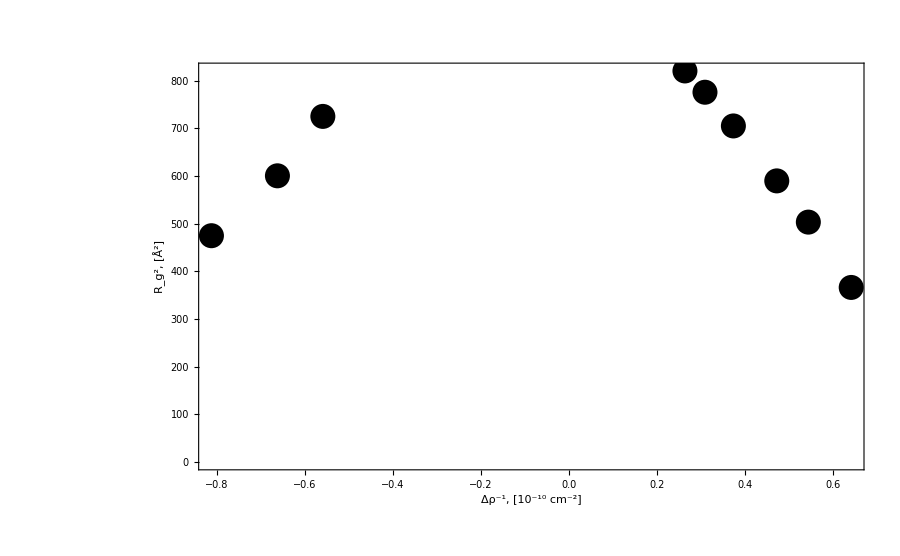

```mathematica
pointswitherrors=ErrorListPlot[pts,PlotStyle->{Black,PointSize[0.02],Thickness[.005]},Epilog->Inset[Style["l",56,Bold],{-1.2,885}],Axes->False,Frame->{{True,False},{True,False}},BaseStyle->{FontFamily->"Times New Roman",20},FrameStyle->Directive[Black,44,Thick],FrameLabel->{Row[{Style["Δρ^-1",FontSlant->Italic],", [10^-10 cm^-2]"}],Row[{Style["R_g^2",FontSlant->Italic], ", [Å^2]"}]},PlotRangeClipping->False,ImageSize->900,PlotRange->All]
```

```mathematica
(*Fitting data*)
```

```mathematica
pointswithouterrors=Sort[Partition[Riffle[inversecontrast,squaredRg],2],#1⟦1⟧<#2⟦1⟧&];
```

```mathematica
nlm=NonlinearModelFit[pointswithouterrors,a+b x+d x^2,{a,b,d},x,Weights->1/errors]
```

FittedModel[932.261-223.472 x-1026.74 x^2]

```mathematica
nlm[{"ParameterTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 932.261 | 14.6042 | 63.835 | 9.9374×10^-10
b | -223.472 | 13.112 | -17.0433 | 2.61012×10^-6
d | -1026.74 | 41.9909 | -24.4515 | 3.07667×10^-7}

```mathematica
(**)
```

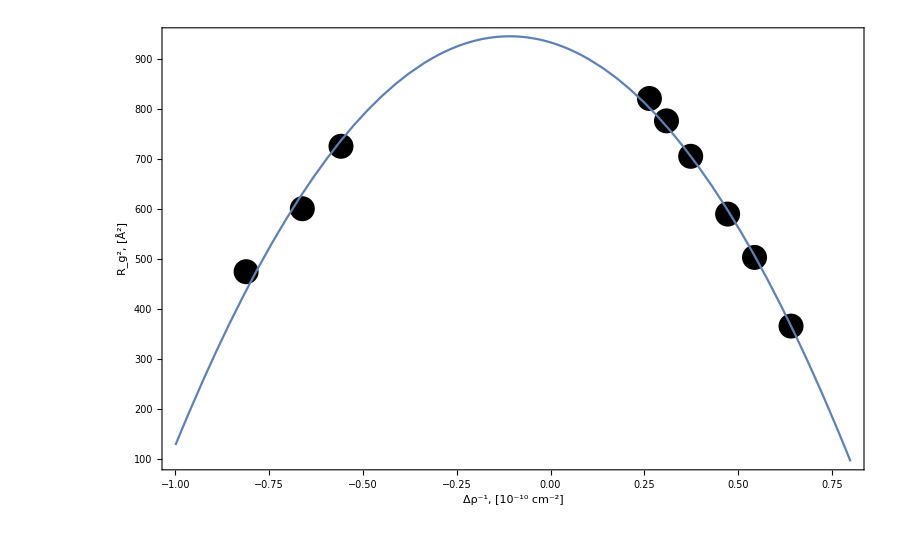

```mathematica
Show[pointswitherrors,Plot[nlm[x],{x,-1,0.8}],PlotRange->All]
```

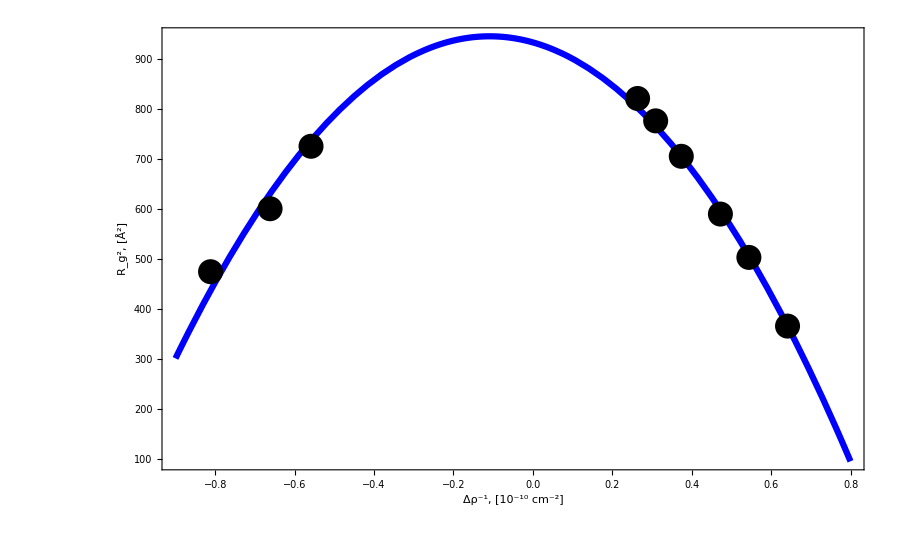

```mathematica
finalplot=Show[Plot[nlm[x],{x,-0.9,0.8},PlotStyle->{Blue,Thickness[0.005]},Axes->False,Epilog->Inset[Style["l",46,Bold],{-1.18,955}],Axes->False,Frame->{{True,False},{True,False}},BaseStyle->{FontFamily->"Times New Roman",20},FrameStyle->Directive[Black,38,Thick],FrameLabel->{Row[{Style["Δρ^-1",FontSlant->Italic],", [10^-10 cm^-2]"}],Row[{Style["R_g^2",FontSlant->Italic], ", [Å^2]"}]},PlotRangeClipping->False,PlotRange->All],pointswitherrors]
```

```mathematica
Export["fig6l.png",finalplot]
```

fig6l.png